```mathematica
mat={{0,1/2,1/2,0},{1/2,0,1/3,1/6},{1/4,1/4,1/4,1/4},{0,1,0,0}};
```

```mathematica
mat//MatrixForm
```

(0 | 1/2 | 1/2 | 0
1/2 | 0 | 1/3 | 1/6
1/4 | 1/4 | 1/4 | 1/4
0 | 1 | 0 | 0)

```mathematica
P=DiscreteMarkovProcess[{1,0,0,0},{{0,1/2,1/2,0},{1/2,0,1/3,1/6},{1/4,1/4,1/4,1/4},{0,1,0,0}}];
```

```mathematica
StationaryDistribution[P]
```

ProbabilityDistribution[11/46 Boole[x==1]+15/46 Boole[x==2]+7/23 Boole[x==3]+3/23 Boole[x==4],{x,1,4,1}]

```mathematica
data=Normal[RandomFunction[P,{0,10000}]][[1]][[All,2]];
```

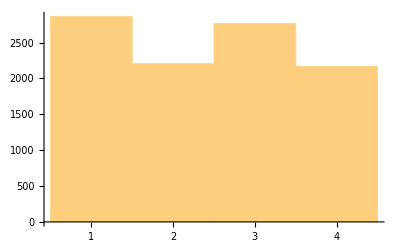

```mathematica
Histogram[data]
```

```mathematica
P1=DiscreteMarkovProcess[{1,0,0,0},{{0,1/2,1/2,0},{1/2,0,1/3,1/6},{1/4,1/4,1/4,1/4},{1/2,0,1/6,1/3}}];
```

```mathematica
StationaryDistribution[P1]
```

ProbabilityDistribution[19/68 Boole[x==1]+15/68 Boole[x==2]+11/34 Boole[x==3]+3/17 Boole[x==4],{x,1,4,1}]

```mathematica
data=Normal[RandomFunction[P1,{0,10000}]][[1]][[All,2]];
```

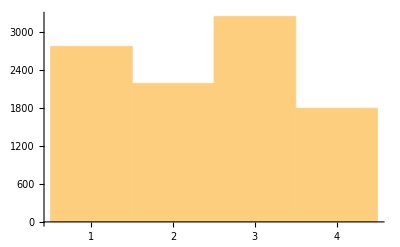

```mathematica
Histogram[data]
```

```mathematica
P2=DiscreteMarkovProcess[{1,0,0,0},{{0,1/2,1/2,0},{1/2,0,1/3,1/6},{1/4,1/4,1/4,1/4},{0,1,0,0}}];
```

```mathematica
data=Normal[RandomFunction[P2,{0,10000}]][[1]][[All,2]];
```

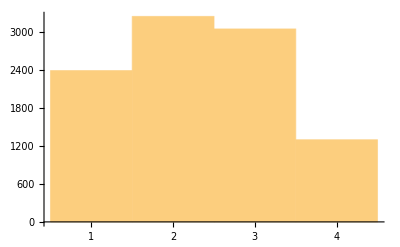

```mathematica
Histogram[data]
```

```mathematica
Rationalize[0.625]
```

5/8

```mathematica
m={{0,1/2,1/2,0},{1/2,0,1/3,1/6},{5/8,1/8,1/8,1/8},{1/2,1/2,0,0}};
m//MatrixForm
```

(0 | 1/2 | 1/2 | 0
1/2 | 0 | 1/3 | 1/6
5/8 | 1/8 | 1/8 | 1/8
1/2 | 1/2 | 0 | 0)

```mathematica
StationaryDistribution[DiscreteMarkovProcess[{1,0,0,0},m]]
```

ProbabilityDistribution[71/198 Boole[x==1]+17/66 Boole[x==2]+10/33 Boole[x==3]+8/99 Boole[x==4],{x,1,4,1}]

```mathematica
m={{0,1/2,1/2,0},{1/2,0,1/3,1/6},{1,0,0,0},{1,0,0,0}};
m//MatrixForm
```

(0 | 1/2 | 1/2 | 0
1/2 | 0 | 1/3 | 1/6
1 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
StationaryDistribution[DiscreteMarkovProcess[{1,0,0,0},m]]
```

ProbabilityDistribution[4/9 Boole[x==1]+2/9 Boole[x==2]+8/27 Boole[x==3]+1/27 Boole[x==4],{x,1,4,1}]